```mathematica
Quit[]
```

## Import packages, set up model and functions

Import MASS toolbox

```mathematica
<<Toolbox`
<<Toolbox`Style`
```

Define working directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Import Smallbone model

```mathematica
modelSmallbone18=sbml2model["MODEL1303260018.xml"];
```

See model structure (no regulation included here)

```mathematica
First@Import["glycolysis_yeast.pdf"]
```

-Graphics-

Define starveSystem function

```mathematica
starveSystem[starveTime_, starveGlc_, originalModel_] := 
 Block[{modelTemp, cSmallbone, fSmallbone},

  modelTemp = originalModel;
  {cSmallbone, fSmallbone} = simulate[modelTemp, {t, 0, starveTime},  Parameters -> {GLCx^extracellular-> starveGlc}]; 
  updateInitialConditions[modelTemp, cSmallbone /. t ->  starveTime];

  Return[{modelTemp, cSmallbone, fSmallbone}];];
```

Define exportData function

```mathematica
exportData[outputFile_,data_, simLength_, timeInterval_:0.001]:=Block[{concDataToExport},

concDataToExport = 
	Table[
		Flatten@{tPoint, Values@data/.t-> tPoint},
	{tPoint, 0, simLength, timeInterval}];

	concDataToExport=Insert[concDataToExport,Flatten@{"t", Map[getID@#&, Keys@data]},1];

	Export[outputFile, concDataToExport, "CSV"];

];
```

## Simulate cell starvation

#### Do starvation simulation

Define starvation time, glucose concentration during starvation, and glucose concentration for the glucose pulse

```mathematica
starveGlc=0.1; (* in mM/L *)
starveTime=1200; (* in seconds *)
```

Starve the model, a new model is returned whose initial metabolite concentrations are the concentrations at the end of the starvation period

```mathematica
{model,concStarv, fluxStarv}=starveSystem[starveTime,starveGlc,modelSmallbone18];
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Export simulation data

```mathematica
exportData["conc_starvation.csv", concStarv, starveTime,0.1];
exportData["flux_starvation.csv", fluxStarv, starveTime,0.1];
```

#### Plot metabolite and flux time courses during starvation

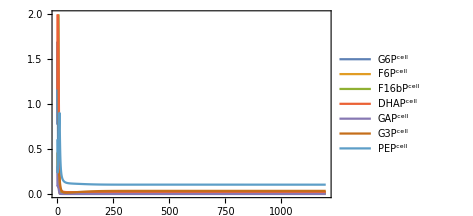

```mathematica
plotSimulation[filter[concStarv,{G6P^cell,F6P^cell,F16bP^cell, DHAP^cell,GAP^cell,G3P^cell,PEP^cell}],PlotFunction->Plot,PlotRange->{{0,1200},{0,2}},Legend->True]
```

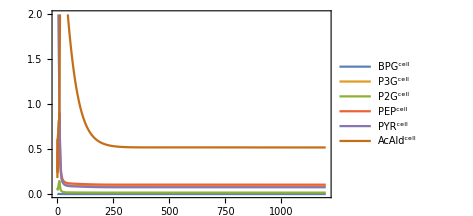

```mathematica
plotSimulation[filter[concStarv,{BPG^cell,P3G^cell,P2G^cell,PEP^cell,PYR^cell,AcAld^cell}],PlotFunction->Plot,PlotRange->{{0,1200},{0,2}},Legend->True]
```

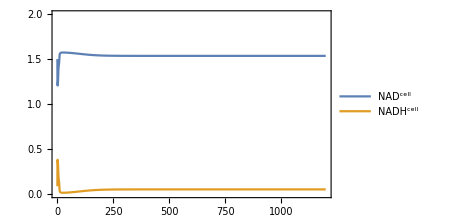

```mathematica
plotSimulation[filter[concStarv,{NAD^cell,NADH^cell}],PlotFunction->Plot,PlotRange->{{0,1200},{0,2}},
Legend->True]
```

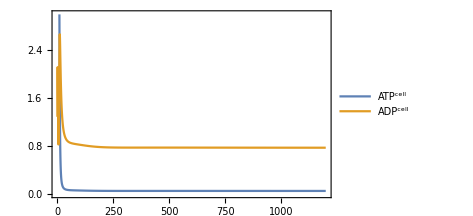

```mathematica
plotSimulation[filter[concStarv,{ATP^cell,ADP^cell}],PlotFunction->Plot,PlotRange->{{0,1200},{0,3}},Legend->True]
```

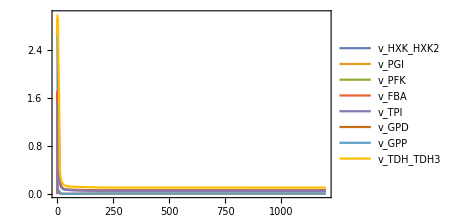

```mathematica
plotSimulation[filter[fluxStarv,{Subscript[v, HXK_HXK2],Subscript[v, PGI],Subscript[v, PFK],Subscript[v, FBA],Subscript[v, TPI],Subscript[v, GPD],Subscript[v, GPP],Subscript[v, TDH_TDH3]}],PlotFunction->Plot,PlotRange->{{0,1200},{0,3}},Legend->True]
```

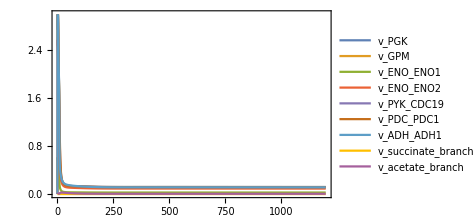

```mathematica
plotSimulation[filter[fluxStarv,{Subscript[v, PGK],Subscript[v, GPM],Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2],Subscript[v, PYK_CDC19],Subscript[v, PDC_PDC1],Subscript[v, ADH_ADH1],Subscript[v, succinate_branch],Subscript[v, acetate_branch]}],PlotFunction->Plot,PlotRange->{{0,1200},{0,3}},Legend->True]
```

## Simulate glucose pulse, with external glucose concentration set to 4 mM

### Simulate the glucose pulse

```mathematica
glcPulse = 4; (*glucose concetration in mmol/L*)
glcPulseSimulationTime = 60; (*in seconds*)
```

```mathematica
{concentrationGlcPulse,fluxGlcPulse}=simulate[model,{t,0,glcPulseSimulationTime},Parameters->{GLCx^extracellular->glcPulse}];
```

Export simulation data

```mathematica
exportData["conc_glc_pulse.csv", concentrationGlcPulse, 60,0.01];
exportData["flux_glc_pulse.csv", fluxGlcPulse, 60,0.01];
```

Plot initial metabolite concentrations, to see which metabolites accumulated during starvation

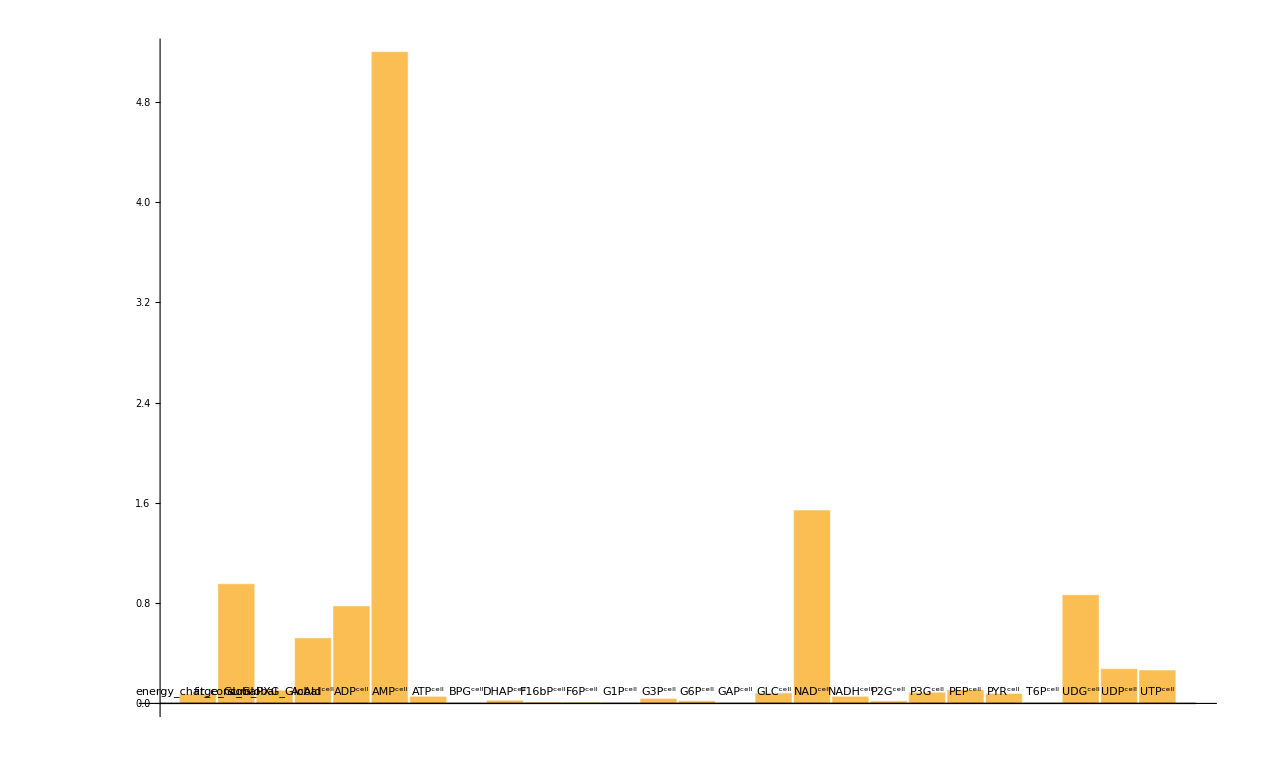

```mathematica
BarChart[Values@model["InitialConditions"], ChartLabels->Placed[Keys@model["InitialConditions"], Bottom]]
```

### Plot simulation results

#### Figure 5B

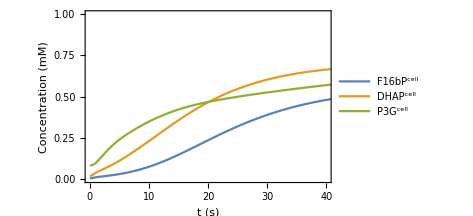

```mathematica
plot=plotSimulation[filter[concentrationGlcPulse,{F16bP^cell, DHAP^cell,P3G^cell}],PlotFunction->Plot,PlotRange->{{0,40},{0,1}},Legend->True, FrameLabel->{"t (s)","Concentration (mM)"}]
```

#### Other simulation results

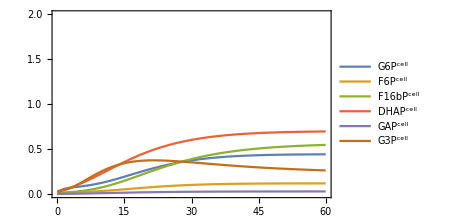

```mathematica
plot=plotSimulation[filter[concentrationGlcPulse,{G6P^cell,F6P^cell,F16bP^cell, DHAP^cell,GAP^cell,G3P^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
```

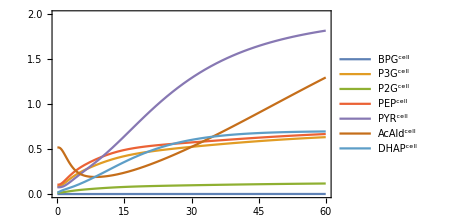

```mathematica
plot=plotSimulation[filter[concentrationGlcPulse,{BPG^cell,P3G^cell,P2G^cell,PEP^cell,PYR^cell,AcAld^cell,DHAP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
```

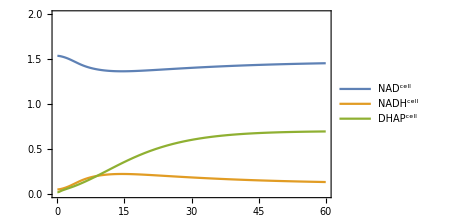

```mathematica
plot=plotSimulation[filter[concentrationGlcPulse,{NAD^cell,NADH^cell,DHAP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,2}},Legend->True]
```

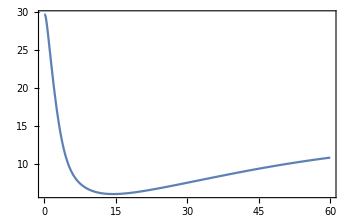

```mathematica
plot=Plot[Values@filter[concentrationGlcPulse,{NAD^cell}]/Values@filter[concentrationGlcPulse,{NADH^cell}], {t,0,60}]
```

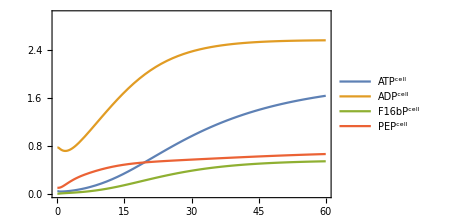

```mathematica
plot=plotSimulation[filter[concentrationGlcPulse,{ATP^cell,ADP^cell,F16bP^cell,PEP^cell}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
```

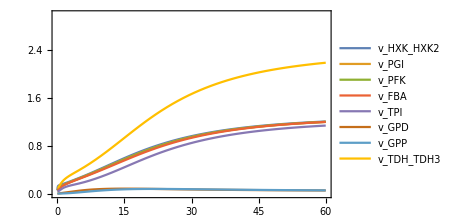

```mathematica
plot=plotSimulation[filter[fluxGlcPulse,{Subscript[v, HXK_HXK2],Subscript[v, PGI],Subscript[v, PFK],Subscript[v, FBA],Subscript[v, TPI],Subscript[v, GPD],Subscript[v, GPP],Subscript[v, TDH_TDH3]}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
```

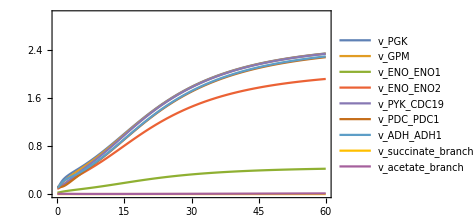

```mathematica
plot=plotSimulation[filter[fluxGlcPulse,{Subscript[v, PGK],Subscript[v, GPM],Subscript[v, ENO_ENO1],Subscript[v, ENO_ENO2],Subscript[v, PYK_CDC19],Subscript[v, PDC_PDC1],Subscript[v, ADH_ADH1],Subscript[v, succinate_branch],Subscript[v, acetate_branch]}],PlotFunction->Plot,PlotRange->{{0,60},{0,3}},Legend->True]
```

## Simulate glucose and acetaldehyde coinjection, with external glucose concentration set to 4 mM and internal acetaldehyde concentration set to 2.3 mM

### Simulate the glucose+acetaldehyde pulse

```mathematica
{concentrationCoinjection1,fluxCoinjection1}=simulate[model,{t,0,60},Parameters->{GLCx^extracellular->4}, InitialConditions->{ AcAld^cell-> 2.3}];
```

Export simulation data

```mathematica
exportData["conc_glc_pulse_acald23.csv", concentrationCoinjection1, 60,0.01];
exportData["flux_glc_pulse_acald23.csv", fluxCoinjection1, 60,0.01];
```

### Plot simulation results

#### Figure S5

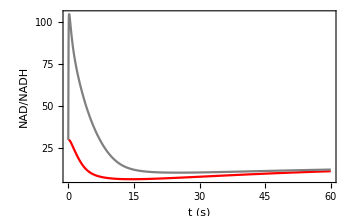

```mathematica
plotGlcPulse=Plot[Values@filter[concentrationGlcPulse,{NAD^cell}]/Values@filter[concentrationGlcPulse,{NADH^cell}], {t,0,60}, PlotStyle->Red];
plotCoinjection=Plot[Values@filter[concentrationCoinjection1,{NAD^cell}]/Values@filter[concentrationCoinjection1,{NADH^cell}], {t,0,60}, PlotStyle->Gray];
Show[plotGlcPulse, plotCoinjection, FrameLabel->{"t (s)","NAD/NADH"}]
```

## Simulate second glucose and acetaldehyde coinjection, with external glucose concentration set to 4 mM and internal acetadehyde concentration set to 12 mM

### Simulate the glucose+acetaldehyde pulse

```mathematica
{concentrationCoinjection2,fluxCoinjection2}=simulate[model,{t,0,60},Parameters->{GLCx^extracellular->4}, InitialConditions->{ AcAld^cell-> 12}];
```

Export simulation data

```mathematica
exportData["conc_glc_pulse_acald12.csv", concentrationCoinjection2, 60,0.01];
exportData["flux_glc_pulse_acald12.csv", fluxCoinjection2, 60,0.01];
```

### Plot simulation results

#### Figure S7 - 3PG evolution

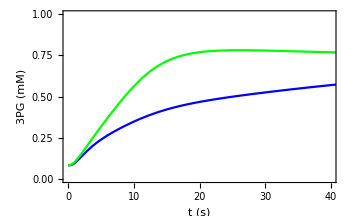

```mathematica
plot3PGnoAcald=plotSimulation[filter[concentrationGlcPulse,{P3G^cell}],PlotFunction->Plot,PlotRange->{{0,40},{0,1}}, PlotStyle-> Blue];
plot3PG12Acald=plotSimulation[filter[concentrationCoinjection2,{P3G^cell}],PlotFunction->Plot,PlotRange->{{0,40},{0,1}}, PlotStyle-> Green];
Show[plot3PGnoAcald,plot3PG12Acald, FrameLabel->{"t (s)","3PG (mM)"}]
```

#### Figure S7 - pyruvate evolution

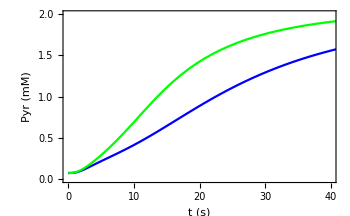

```mathematica
plotPYRnoAcald=plotSimulation[filter[concentrationGlcPulse,{PYR^cell}],PlotFunction->Plot,PlotRange->{{0,40},{0,2}}, PlotStyle-> Blue];
plotPYR12Acald=plotSimulation[filter[concentrationCoinjection2,{PYR^cell}],PlotFunction->Plot,PlotRange->{{0,40},{0,2}}, PlotStyle-> Green];
Show[plotPYRnoAcald,plotPYR12Acald, FrameLabel->{"t (s)","Pyr (mM)"}]
```

#### Figure S7 - GrnP evolution

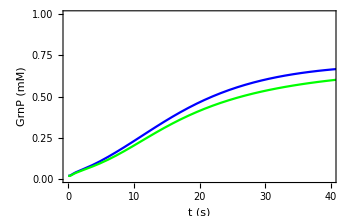

```mathematica
plotGrnPnoAcald=plotSimulation[filter[concentrationGlcPulse,{DHAP^cell}],PlotFunction->Plot,PlotRange->{{0,40},{0,1}}, PlotStyle-> Blue];
plotGrnP12Acald=plotSimulation[filter[concentrationCoinjection2,{DHAP^cell}],PlotFunction->Plot,PlotRange->{{0,40},{0,1}}, PlotStyle-> Green];
Show[plotGrnPnoAcald,plotGrnP12Acald,FrameLabel->{"t (s)","GrnP (mM)"}]
```

## Energy charge ratio = 0.37: set ADP = 3.01, and ADP/ATP ratio = 4

### Simulate glucose pusel with energy charge and acetaldehyde increase

```mathematica
{concentrationEnergyCharge,fluxEnergyCharge}=simulate[model,{t,0,60},InitialConditions-> {ADP^cell->3.01, ATP^cell->0.75 ,AcAld^cell->1.6426428464870837},Parameters->{GLCx^extracellular->4}];
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

Export simulation data

```mathematica
exportData["conc_glc_pulse_S6.csv", concentrationEnergyCharge, 60,0.01];
exportData["flux_glc_pulse_S6.csv", fluxEnergyCharge, 60,0.01];
```

### Plot simulation results

#### Figure S6

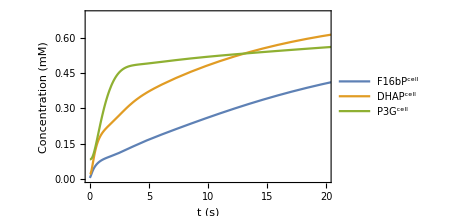

```mathematica
plot=plotSimulation[
filter[concentrationEnergyCharge,{F16bP^cell,DHAP^cell,P3G^cell}],FrameLabel->{"t (s)","Concentration (mM)"},PlotFunction->Plot,PlotRange->{{0,20},{0,0.7}},Legend->True]
```

### Simulation without AcAld increase

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

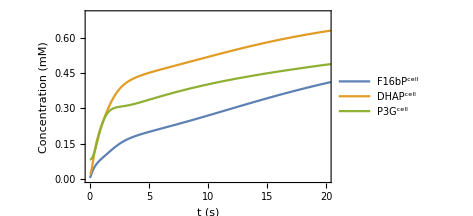

```mathematica
{concentrationEnergyChargeNoAcaldChange,fluxEnergyChargeNoAcaldChange}=simulate[model,{t,0,60},InitialConditions-> {ADP^cell->3.01, ATP^cell->0.75 },Parameters->{GLCx^extracellular->4}];

plot=plotSimulation[
filter[concentrationEnergyChargeNoAcaldChange,{F16bP^cell,DHAP^cell,P3G^cell}],FrameLabel->{"t (s)","Concentration (mM)"},PlotFunction->Plot,PlotRange->{{0,20},{0,0.7}},Legend->True]
```